# Bistable motif: parameter sampling

## Finding the condition of multistationarity

We consider the following reactions:

K+S⇋KS→K+S_p
K^✶+S⇋K^✶S→K^✶+S_p
S_p→S
K⇋K^✶
KS⇋K^✶S

The species of the system are:

{S,S_p,K,K^✶,KS,K^✶S}

In total, there are 11 reations and 6 species.

We firstly construct the ordinary differential equations based on mass-action kinetics. Then compute the determinant of Jacobian, using the solution at critical point (steady state) to calculate the determinant. The (necessary) condition for multistationarity is to make determinant equal to zero (non-zero determinant implys injectivity).

```mathematica
A=Table[0,{11},{6}];
A[[1]][[1]]=-1;A[[1]][[3]]=-1;A[[1]][[5]]=1;A[[2]]=-A[[1]];
A[[3]][[3]]=1;A[[3]][[2]]=1;A[[3]][[5]]=-1;
A[[4]][[1]]=-1;A[[4]][[4]]=-1;A[[4]][[6]]=1;A[[5]]=-A[[4]];
A[[6]][[4]]=1;A[[6]][[2]]=1;A[[6]][[6]]=-1;A[[7]][[2]]=-1;A[[7]][[1]]=1;
A[[8]][[3]]=-1;A[[8]][[4]]=1;A[[9]]=-A[[8]];
A[[10]][[5]]=-1;A[[10]][[6]]=1;A[[11]]=-A[[10]];
stoiM=Transpose[A];
(* Now we construct the rate vector *)
ks={Subscript[k, 1]×Subscript[x, 3]×Subscript[x, 1],Subscript[k, 2]×Subscript[x, 5],Subscript[k, 3]×Subscript[x, 5],Subscript[k, 4]×Subscript[x, 4]×Subscript[x, 1],Subscript[k, 5]×Subscript[x, 6],Subscript[k, 6]×Subscript[x, 6],Subscript[k, 7]×Subscript[x, 2],Subscript[k, 8]×Subscript[x, 3],Subscript[k, 9]×Subscript[x, 4],Subscript[k, 10]×Subscript[x, 5],Subscript[k, 11]×Subscript[x, 6]};
ssEqns=stoiM.ks;
mC=RowReduce[NullSpace[A]];
subsEqns={ssEqns[[2]],ssEqns[[4]],ssEqns[[5]],ssEqns[[6]],Subscript[x, 1]+Subscript[x, 2]+Subscript[x, 5]+Subscript[x, 6]-Subscript[T, 1],Subscript[x, 3]+Subscript[x, 4]+Subscript[x, 5]+Subscript[x, 6]-Subscript[T, 2]};
jacobian=D[subsEqns,{{Subscript[x, 1],Subscript[x, 2],Subscript[x, 3],Subscript[x, 4],Subscript[x, 5],Subscript[x, 6]}}];
detJ=Collect[Distribute[Det[jacobian]],{Subscript[x, 1],Subscript[x, 2],Subscript[x, 3],Subscript[x, 4],Subscript[x, 5],Subscript[x, 6]}];
solution=Solve[{{subsEqns[[1]],subsEqns[[2]],subsEqns[[3]],subsEqns[[4]]}==0},{Subscript[x, 2],Subscript[x, 4],Subscript[x, 5],Subscript[x, 6]}];
detSubs=Replace[detJ,solution[[1]],{0,Infinity}];  (* Equivilant to detSubs=detJ/.solution[[1]]; *)
polSubs=Numerator[Together[detSubs]];
finalSubs=Collect[Distribute[polSubs],Subscript[x, _],FactorTerms]
```

-k_2^2 k_5^2 k_7 k_8 k_9-2 k_2 k_3 k_5^2 k_7 k_8 k_9-k_3^2 k_5^2 k_7 k_8 k_9-2 k_2^2 k_5 k_6 k_7 k_8 k_9-4 k_2 k_3 k_5 k_6 k_7 k_8 k_9-2 k_3^2 k_5 k_6 k_7 k_8 k_9-k_2^2 k_6^2 k_7 k_8 k_9-2 k_2 k_3 k_6^2 k_7 k_8 k_9-k_3^2 k_6^2 k_7 k_8 k_9-k_2^2 k_5^2 k_7 k_9^2-2 k_2 k_3 k_5^2 k_7 k_9^2-k_3^2 k_5^2 k_7 k_9^2-2 k_2^2 k_5 k_6 k_7 k_9^2-4 k_2 k_3 k_5 k_6 k_7 k_9^2-2 k_3^2 k_5 k_6 k_7 k_9^2-k_2^2 k_6^2 k_7 k_9^2-2 k_2 k_3 k_6^2 k_7 k_9^2-k_3^2 k_6^2 k_7 k_9^2-2 k_2 k_5^2 k_7 k_8 k_9 k_10-2 k_3 k_5^2 k_7 k_8 k_9 k_10-4 k_2 k_5 k_6 k_7 k_8 k_9 k_10-4 k_3 k_5 k_6 k_7 k_8 k_9 k_10-2 k_2 k_6^2 k_7 k_8 k_9 k_10-2 k_3 k_6^2 k_7 k_8 k_9 k_10-2 k_2 k_5^2 k_7 k_9^2 k_10-2 k_3 k_5^2 k_7 k_9^2 k_10-4 k_2 k_5 k_6 k_7 k_9^2 k_10-4 k_3 k_5 k_6 k_7 k_9^2 k_10-2 k_2 k_6^2 k_7 k_9^2 k_10-2 k_3 k_6^2 k_7 k_9^2 k_10-k_5^2 k_7 k_8 k_9 k_10^2-2 k_5 k_6 k_7 k_8 k_9 k_10^2-k_6^2 k_7 k_8 k_9 k_10^2-k_5^2 k_7 k_9^2 k_10^2-2 k_5 k_6 k_7 k_9^2 k_10^2-k_6^2 k_7 k_9^2 k_10^2-2 k_2^2 k_5 k_7 k_8 k_9 k_11-4 k_2 k_3 k_5 k_7 k_8 k_9 k_11-2 k_3^2 k_5 k_7 k_8 k_9 k_11-2 k_2^2 k_6 k_7 k_8 k_9 k_11-4 k_2 k_3 k_6 k_7 k_8 k_9 k_11-2 k_3^2 k_6 k_7 k_8 k_9 k_11-2 k_2^2 k_5 k_7 k_9^2 k_11-4 k_2 k_3 k_5 k_7 k_9^2 k_11-2 k_3^2 k_5 k_7 k_9^2 k_11-2 k_2^2 k_6 k_7 k_9^2 k_11-4 k_2 k_3 k_6 k_7 k_9^2 k_11-2 k_3^2 k_6 k_7 k_9^2 k_11-2 k_2 k_5 k_7 k_8 k_9 k_10 k_11-2 k_3 k_5 k_7 k_8 k_9 k_10 k_11-2 k_2 k_6 k_7 k_8 k_9 k_10 k_11-2 k_3 k_6 k_7 k_8 k_9 k_10 k_11-2 k_2 k_5 k_7 k_9^2 k_10 k_11-2 k_3 k_5 k_7 k_9^2 k_10 k_11-2 k_2 k_6 k_7 k_9^2 k_10 k_11-2 k_3 k_6 k_7 k_9^2 k_10 k_11-k_2^2 k_7 k_8 k_9 k_11^2-2 k_2 k_3 k_7 k_8 k_9 k_11^2-k_3^2 k_7 k_8 k_9 k_11^2-k_2^2 k_7 k_9^2 k_11^2-2 k_2 k_3 k_7 k_9^2 k_11^2-k_3^2 k_7 k_9^2 k_11^2+(-k_1 k_2 k_4^2 k_7 k_10 k_11-k_1 k_3 k_4^2 k_7 k_10 k_11-k_1 k_2 k_4^2 k_7 k_11^2-k_1 k_3 k_4^2 k_7 k_11^2) x_1^3+(-k_2^2 k_4 k_5 k_6 k_8^2-2 k_2 k_3 k_4 k_5 k_6 k_8^2-k_3^2 k_4 k_5 k_6 k_8^2-k_2^2 k_4 k_6^2 k_8^2-2 k_2 k_3 k_4 k_6^2 k_8^2-k_3^2 k_4 k_6^2 k_8^2-k_2^2 k_4 k_5 k_7 k_8^2-2 k_2 k_3 k_4 k_5 k_7 k_8^2-k_3^2 k_4 k_5 k_7 k_8^2-k_2^2 k_4 k_6 k_7 k_8^2-2 k_2 k_3 k_4 k_6 k_7 k_8^2-k_3^2 k_4 k_6 k_7 k_8^2-k_1 k_2 k_3 k_5^2 k_8 k_9-k_1 k_3^2 k_5^2 k_8 k_9-2 k_1 k_2 k_3 k_5 k_6 k_8 k_9-2 k_1 k_3^2 k_5 k_6 k_8 k_9-k_2^2 k_4 k_5 k_6 k_8 k_9-2 k_2 k_3 k_4 k_5 k_6 k_8 k_9-k_3^2 k_4 k_5 k_6 k_8 k_9-k_1 k_2 k_3 k_6^2 k_8 k_9-k_1 k_3^2 k_6^2 k_8 k_9-k_2^2 k_4 k_6^2 k_8 k_9-2 k_2 k_3 k_4 k_6^2 k_8 k_9-k_3^2 k_4 k_6^2 k_8 k_9-k_2^2 k_4 k_5 k_7 k_8 k_9-2 k_2 k_3 k_4 k_5 k_7 k_8 k_9-k_3^2 k_4 k_5 k_7 k_8 k_9-k_1 k_2 k_5^2 k_7 k_8 k_9-k_1 k_3 k_5^2 k_7 k_8 k_9-k_2^2 k_4 k_6 k_7 k_8 k_9-2 k_2 k_3 k_4 k_6 k_7 k_8 k_9-k_3^2 k_4 k_6 k_7 k_8 k_9-2 k_1 k_2 k_5 k_6 k_7 k_8 k_9-2 k_1 k_3 k_5 k_6 k_7 k_8 k_9-k_1 k_2 k_6^2 k_7 k_8 k_9-k_1 k_3 k_6^2 k_7 k_8 k_9-k_1 k_2 k_3 k_5^2 k_9^2-k_1 k_3^2 k_5^2 k_9^2-2 k_1 k_2 k_3 k_5 k_6 k_9^2-2 k_1 k_3^2 k_5 k_6 k_9^2-k_1 k_2 k_3 k_6^2 k_9^2-k_1 k_3^2 k_6^2 k_9^2-k_1 k_2 k_5^2 k_7 k_9^2-k_1 k_3 k_5^2 k_7 k_9^2-2 k_1 k_2 k_5 k_6 k_7 k_9^2-2 k_1 k_3 k_5 k_6 k_7 k_9^2-k_1 k_2 k_6^2 k_7 k_9^2-k_1 k_3 k_6^2 k_7 k_9^2-2 k_2 k_4 k_5 k_6 k_8^2 k_10-2 k_3 k_4 k_5 k_6 k_8^2 k_10-2 k_2 k_4 k_6^2 k_8^2 k_10-2 k_3 k_4 k_6^2 k_8^2 k_10-2 k_2 k_4 k_5 k_7 k_8^2 k_10-2 k_3 k_4 k_5 k_7 k_8^2 k_10-2 k_2 k_4 k_6 k_7 k_8^2 k_10-2 k_3 k_4 k_6 k_7 k_8^2 k_10-k_1 k_3 k_5^2 k_8 k_9 k_10-k_1 k_2 k_5 k_6 k_8 k_9 k_10-3 k_1 k_3 k_5 k_6 k_8 k_9 k_10-2 k_2 k_4 k_5 k_6 k_8 k_9 k_10-2 k_3 k_4 k_5 k_6 k_8 k_9 k_10-k_1 k_2 k_6^2 k_8 k_9 k_10-2 k_1 k_3 k_6^2 k_8 k_9 k_10-2 k_2 k_4 k_6^2 k_8 k_9 k_10-2 k_3 k_4 k_6^2 k_8 k_9 k_10-k_1 k_2 k_5 k_7 k_8 k_9 k_10-k_1 k_3 k_5 k_7 k_8 k_9 k_10-2 k_2 k_4 k_5 k_7 k_8 k_9 k_10-2 k_3 k_4 k_5 k_7 k_8 k_9 k_10-k_1 k_5^2 k_7 k_8 k_9 k_10-k_1 k_2 k_6 k_7 k_8 k_9 k_10-k_1 k_3 k_6 k_7 k_8 k_9 k_10-2 k_2 k_4 k_6 k_7 k_8 k_9 k_10-2 k_3 k_4 k_6 k_7 k_8 k_9 k_10-2 k_1 k_5 k_6 k_7 k_8 k_9 k_10-k_1 k_6^2 k_7 k_8 k_9 k_10-k_1 k_3 k_5^2 k_9^2 k_10-k_1 k_2 k_5 k_6 k_9^2 k_10-3 k_1 k_3 k_5 k_6 k_9^2 k_10-k_1 k_2 k_6^2 k_9^2 k_10-2 k_1 k_3 k_6^2 k_9^2 k_10-k_1 k_2 k_5 k_7 k_9^2 k_10-k_1 k_3 k_5 k_7 k_9^2 k_10-k_1 k_5^2 k_7 k_9^2 k_10-k_1 k_2 k_6 k_7 k_9^2 k_10-k_1 k_3 k_6 k_7 k_9^2 k_10-2 k_1 k_5 k_6 k_7 k_9^2 k_10-k_1 k_6^2 k_7 k_9^2 k_10-k_4 k_5 k_6 k_8^2 k_10^2-k_4 k_6^2 k_8^2 k_10^2-k_4 k_5 k_7 k_8^2 k_10^2-k_4 k_6 k_7 k_8^2 k_10^2-k_1 k_5 k_6 k_8 k_9 k_10^2-k_4 k_5 k_6 k_8 k_9 k_10^2-k_1 k_6^2 k_8 k_9 k_10^2-k_4 k_6^2 k_8 k_9 k_10^2-k_1 k_5 k_7 k_8 k_9 k_10^2-k_4 k_5 k_7 k_8 k_9 k_10^2-k_1 k_6 k_7 k_8 k_9 k_10^2-k_4 k_6 k_7 k_8 k_9 k_10^2-k_1 k_5 k_6 k_9^2 k_10^2-k_1 k_6^2 k_9^2 k_10^2-k_1 k_5 k_7 k_9^2 k_10^2-k_1 k_6 k_7 k_9^2 k_10^2-k_2 k_3 k_4 k_5 k_8^2 k_11-k_3^2 k_4 k_5 k_8^2 k_11-k_2^2 k_4 k_6 k_8^2 k_11-3 k_2 k_3 k_4 k_6 k_8^2 k_11-2 k_3^2 k_4 k_6 k_8^2 k_11-k_2^2 k_4 k_7 k_8^2 k_11-2 k_2 k_3 k_4 k_7 k_8^2 k_11-k_3^2 k_4 k_7 k_8^2 k_11-k_2 k_4 k_5 k_7 k_8^2 k_11-k_3 k_4 k_5 k_7 k_8^2 k_11-k_2 k_4 k_6 k_7 k_8^2 k_11-k_3 k_4 k_6 k_7 k_8^2 k_11-2 k_1 k_2 k_3 k_5 k_8 k_9 k_11-2 k_1 k_3^2 k_5 k_8 k_9 k_11-k_2 k_3 k_4 k_5 k_8 k_9 k_11-k_3^2 k_4 k_5 k_8 k_9 k_11-2 k_1 k_2 k_3 k_6 k_8 k_9 k_11-2 k_1 k_3^2 k_6 k_8 k_9 k_11-k_2^2 k_4 k_6 k_8 k_9 k_11-3 k_2 k_3 k_4 k_6 k_8 k_9 k_11-2 k_3^2 k_4 k_6 k_8 k_9 k_11-k_2^2 k_4 k_7 k_8 k_9 k_11-2 k_2 k_3 k_4 k_7 k_8 k_9 k_11-k_3^2 k_4 k_7 k_8 k_9 k_11-2 k_1 k_2 k_5 k_7 k_8 k_9 k_11-2 k_1 k_3 k_5 k_7 k_8 k_9 k_11-k_2 k_4 k_5 k_7 k_8 k_9 k_11-k_3 k_4 k_5 k_7 k_8 k_9 k_11-2 k_1 k_2 k_6 k_7 k_8 k_9 k_11-2 k_1 k_3 k_6 k_7 k_8 k_9 k_11-k_2 k_4 k_6 k_7 k_8 k_9 k_11-k_3 k_4 k_6 k_7 k_8 k_9 k_11-2 k_1 k_2 k_3 k_5 k_9^2 k_11-2 k_1 k_3^2 k_5 k_9^2 k_11-2 k_1 k_2 k_3 k_6 k_9^2 k_11-2 k_1 k_3^2 k_6 k_9^2 k_11-2 k_1 k_2 k_5 k_7 k_9^2 k_11-2 k_1 k_3 k_5 k_7 k_9^2 k_11-2 k_1 k_2 k_6 k_7 k_9^2 k_11-2 k_1 k_3 k_6 k_7 k_9^2 k_11-k_3 k_4 k_5 k_8^2 k_10 k_11-k_2 k_4 k_6 k_8^2 k_10 k_11-2 k_3 k_4 k_6 k_8^2 k_10 k_11-k_2 k_4 k_7 k_8^2 k_10 k_11-k_3 k_4 k_7 k_8^2 k_10 k_11-k_4 k_5 k_7 k_8^2 k_10 k_11-k_4 k_6 k_7 k_8^2 k_10 k_11-k_1 k_3 k_5 k_8 k_9 k_10 k_11-k_3 k_4 k_5 k_8 k_9 k_10 k_11-k_1 k_2 k_6 k_8 k_9 k_10 k_11-2 k_1 k_3 k_6 k_8 k_9 k_10 k_11-k_2 k_4 k_6 k_8 k_9 k_10 k_11-2 k_3 k_4 k_6 k_8 k_9 k_10 k_11-k_1 k_2 k_7 k_8 k_9 k_10 k_11-k_1 k_3 k_7 k_8 k_9 k_10 k_11-k_2 k_4 k_7 k_8 k_9 k_10 k_11-k_3 k_4 k_7 k_8 k_9 k_10 k_11-k_1 k_5 k_7 k_8 k_9 k_10 k_11-k_4 k_5 k_7 k_8 k_9 k_10 k_11-k_1 k_6 k_7 k_8 k_9 k_10 k_11-k_4 k_6 k_7 k_8 k_9 k_10 k_11-k_1 k_3 k_5 k_9^2 k_10 k_11-k_1 k_2 k_6 k_9^2 k_10 k_11-2 k_1 k_3 k_6 k_9^2 k_10 k_11-k_1 k_2 k_7 k_9^2 k_10 k_11-k_1 k_3 k_7 k_9^2 k_10 k_11-k_1 k_5 k_7 k_9^2 k_10 k_11-k_1 k_6 k_7 k_9^2 k_10 k_11-k_2 k_3 k_4 k_8^2 k_11^2-k_3^2 k_4 k_8^2 k_11^2-k_2 k_4 k_7 k_8^2 k_11^2-k_3 k_4 k_7 k_8^2 k_11^2-k_1 k_2 k_3 k_8 k_9 k_11^2-k_1 k_3^2 k_8 k_9 k_11^2-k_2 k_3 k_4 k_8 k_9 k_11^2-k_3^2 k_4 k_8 k_9 k_11^2-k_1 k_2 k_7 k_8 k_9 k_11^2-k_1 k_3 k_7 k_8 k_9 k_11^2-k_2 k_4 k_7 k_8 k_9 k_11^2-k_3 k_4 k_7 k_8 k_9 k_11^2-k_1 k_2 k_3 k_9^2 k_11^2-k_1 k_3^2 k_9^2 k_11^2-k_1 k_2 k_7 k_9^2 k_11^2-k_1 k_3 k_7 k_9^2 k_11^2) x_3+x_1^2 (-k_1 k_2 k_4 k_5 k_7 k_9 k_10-k_1 k_3 k_4 k_5 k_7 k_9 k_10-k_1 k_2 k_4 k_6 k_7 k_9 k_10-k_1 k_3 k_4 k_6 k_7 k_9 k_10-k_1 k_4 k_5 k_7 k_9 k_10^2-k_1 k_4 k_6 k_7 k_9 k_10^2-k_2^2 k_4^2 k_7 k_8 k_11-2 k_2 k_3 k_4^2 k_7 k_8 k_11-k_3^2 k_4^2 k_7 k_8 k_11-2 k_1 k_2 k_4 k_5 k_7 k_9 k_11-2 k_1 k_3 k_4 k_5 k_7 k_9 k_11-2 k_1 k_2 k_4 k_6 k_7 k_9 k_11-2 k_1 k_3 k_4 k_6 k_7 k_9 k_11-k_1 k_2 k_4 k_5 k_7 k_10 k_11-k_1 k_3 k_4 k_5 k_7 k_10 k_11-k_1 k_2 k_4 k_6 k_7 k_10 k_11-k_1 k_3 k_4 k_6 k_7 k_10 k_11-k_2 k_4^2 k_7 k_8 k_10 k_11-k_3 k_4^2 k_7 k_8 k_10 k_11-2 k_1 k_2 k_4 k_7 k_9 k_10 k_11-2 k_1 k_3 k_4 k_7 k_9 k_10 k_11-k_1 k_4 k_5 k_7 k_9 k_10 k_11-k_1 k_4 k_6 k_7 k_9 k_10 k_11-k_2^2 k_4^2 k_7 k_11^2-2 k_2 k_3 k_4^2 k_7 k_11^2-k_3^2 k_4^2 k_7 k_11^2-k_2 k_4^2 k_7 k_8 k_11^2-k_3 k_4^2 k_7 k_8 k_11^2-2 k_1 k_2 k_4 k_7 k_9 k_11^2-2 k_1 k_3 k_4 k_7 k_9 k_11^2+(k_1^2 k_3 k_4 k_5 k_9 k_10+k_1^2 k_3 k_4 k_6 k_9 k_10-k_1^2 k_4 k_5 k_6 k_9 k_10-k_1^2 k_4 k_6^2 k_9 k_10-k_1^2 k_4 k_5 k_6 k_10^2-k_1^2 k_4 k_6^2 k_10^2-k_1^2 k_4 k_5 k_7 k_10^2-k_1^2 k_4 k_6 k_7 k_10^2-k_1 k_2 k_3 k_4^2 k_8 k_11-k_1 k_3^2 k_4^2 k_8 k_11+k_1 k_2 k_4^2 k_6 k_8 k_11+k_1 k_3 k_4^2 k_6 k_8 k_11-k_1^2 k_3 k_4 k_5 k_10 k_11-k_1^2 k_3 k_4 k_6 k_10 k_11-k_1 k_2 k_4^2 k_6 k_10 k_11-k_1 k_3 k_4^2 k_6 k_10 k_11-k_1 k_2 k_4^2 k_7 k_10 k_11-k_1 k_3 k_4^2 k_7 k_10 k_11-k_1^2 k_4 k_5 k_7 k_10 k_11-k_1^2 k_4 k_6 k_7 k_10 k_11-k_1 k_2 k_3 k_4^2 k_11^2-k_1 k_3^2 k_4^2 k_11^2-k_1 k_2 k_4^2 k_7 k_11^2-k_1 k_3 k_4^2 k_7 k_11^2) x_3)+x_1 (-k_2^2 k_4 k_5 k_7 k_8 k_9-2 k_2 k_3 k_4 k_5 k_7 k_8 k_9-k_3^2 k_4 k_5 k_7 k_8 k_9-k_2^2 k_4 k_6 k_7 k_8 k_9-2 k_2 k_3 k_4 k_6 k_7 k_8 k_9-k_3^2 k_4 k_6 k_7 k_8 k_9-k_1 k_2 k_5^2 k_7 k_9^2-k_1 k_3 k_5^2 k_7 k_9^2-2 k_1 k_2 k_5 k_6 k_7 k_9^2-2 k_1 k_3 k_5 k_6 k_7 k_9^2-k_1 k_2 k_6^2 k_7 k_9^2-k_1 k_3 k_6^2 k_7 k_9^2-k_1 k_2 k_5^2 k_7 k_9 k_10-k_1 k_3 k_5^2 k_7 k_9 k_10-2 k_1 k_2 k_5 k_6 k_7 k_9 k_10-2 k_1 k_3 k_5 k_6 k_7 k_9 k_10-k_1 k_2 k_6^2 k_7 k_9 k_10-k_1 k_3 k_6^2 k_7 k_9 k_10-2 k_2 k_4 k_5 k_7 k_8 k_9 k_10-2 k_3 k_4 k_5 k_7 k_8 k_9 k_10-2 k_2 k_4 k_6 k_7 k_8 k_9 k_10-2 k_3 k_4 k_6 k_7 k_8 k_9 k_10-k_1 k_2 k_5 k_7 k_9^2 k_10-k_1 k_3 k_5 k_7 k_9^2 k_10-k_1 k_5^2 k_7 k_9^2 k_10-k_1 k_2 k_6 k_7 k_9^2 k_10-k_1 k_3 k_6 k_7 k_9^2 k_10-2 k_1 k_5 k_6 k_7 k_9^2 k_10-k_1 k_6^2 k_7 k_9^2 k_10-k_1 k_5^2 k_7 k_9 k_10^2-2 k_1 k_5 k_6 k_7 k_9 k_10^2-k_1 k_6^2 k_7 k_9 k_10^2-k_4 k_5 k_7 k_8 k_9 k_10^2-k_4 k_6 k_7 k_8 k_9 k_10^2-k_1 k_5 k_7 k_9^2 k_10^2-k_1 k_6 k_7 k_9^2 k_10^2-k_2^2 k_4 k_5 k_7 k_8 k_11-2 k_2 k_3 k_4 k_5 k_7 k_8 k_11-k_3^2 k_4 k_5 k_7 k_8 k_11-k_2^2 k_4 k_6 k_7 k_8 k_11-2 k_2 k_3 k_4 k_6 k_7 k_8 k_11-k_3^2 k_4 k_6 k_7 k_8 k_11-2 k_2^2 k_4 k_5 k_7 k_9 k_11-4 k_2 k_3 k_4 k_5 k_7 k_9 k_11-2 k_3^2 k_4 k_5 k_7 k_9 k_11-2 k_2^2 k_4 k_6 k_7 k_9 k_11-4 k_2 k_3 k_4 k_6 k_7 k_9 k_11-2 k_3^2 k_4 k_6 k_7 k_9 k_11-k_2^2 k_4 k_7 k_8 k_9 k_11-2 k_2 k_3 k_4 k_7 k_8 k_9 k_11-k_3^2 k_4 k_7 k_8 k_9 k_11-k_2 k_4 k_5 k_7 k_8 k_9 k_11-k_3 k_4 k_5 k_7 k_8 k_9 k_11-k_2 k_4 k_6 k_7 k_8 k_9 k_11-k_3 k_4 k_6 k_7 k_8 k_9 k_11-2 k_1 k_2 k_5 k_7 k_9^2 k_11-2 k_1 k_3 k_5 k_7 k_9^2 k_11-2 k_1 k_2 k_6 k_7 k_9^2 k_11-2 k_1 k_3 k_6 k_7 k_9^2 k_11-k_2 k_4 k_5 k_7 k_8 k_10 k_11-k_3 k_4 k_5 k_7 k_8 k_10 k_11-k_2 k_4 k_6 k_7 k_8 k_10 k_11-k_3 k_4 k_6 k_7 k_8 k_10 k_11-k_1 k_2 k_5 k_7 k_9 k_10 k_11-k_1 k_3 k_5 k_7 k_9 k_10 k_11-2 k_2 k_4 k_5 k_7 k_9 k_10 k_11-2 k_3 k_4 k_5 k_7 k_9 k_10 k_11-k_1 k_2 k_6 k_7 k_9 k_10 k_11-k_1 k_3 k_6 k_7 k_9 k_10 k_11-2 k_2 k_4 k_6 k_7 k_9 k_10 k_11-2 k_3 k_4 k_6 k_7 k_9 k_10 k_11-k_2 k_4 k_7 k_8 k_9 k_10 k_11-k_3 k_4 k_7 k_8 k_9 k_10 k_11-k_4 k_5 k_7 k_8 k_9 k_10 k_11-k_4 k_6 k_7 k_8 k_9 k_10 k_11-k_1 k_2 k_7 k_9^2 k_10 k_11-k_1 k_3 k_7 k_9^2 k_10 k_11-k_1 k_5 k_7 k_9^2 k_10 k_11-k_1 k_6 k_7 k_9^2 k_10 k_11-k_2^2 k_4 k_7 k_8 k_11^2-2 k_2 k_3 k_4 k_7 k_8 k_11^2-k_3^2 k_4 k_7 k_8 k_11^2-2 k_2^2 k_4 k_7 k_9 k_11^2-4 k_2 k_3 k_4 k_7 k_9 k_11^2-2 k_3^2 k_4 k_7 k_9 k_11^2-k_2 k_4 k_7 k_8 k_9 k_11^2-k_3 k_4 k_7 k_8 k_9 k_11^2-k_1 k_2 k_7 k_9^2 k_11^2-k_1 k_3 k_7 k_9^2 k_11^2-2 (k_1 k_2 k_4 k_5 k_6 k_8 k_10+k_1 k_3 k_4 k_5 k_6 k_8 k_10+k_1 k_2 k_4 k_6^2 k_8 k_10+k_1 k_3 k_4 k_6^2 k_8 k_10+k_1 k_2 k_4 k_5 k_7 k_8 k_10+k_1 k_3 k_4 k_5 k_7 k_8 k_10+k_1 k_2 k_4 k_6 k_7 k_8 k_10+k_1 k_3 k_4 k_6 k_7 k_8 k_10+k_1 k_2 k_4 k_5 k_6 k_9 k_10+k_1 k_3 k_4 k_5 k_6 k_9 k_10+k_1 k_2 k_4 k_6^2 k_9 k_10+k_1 k_3 k_4 k_6^2 k_9 k_10+k_1 k_2 k_4 k_5 k_7 k_9 k_10+k_1 k_3 k_4 k_5 k_7 k_9 k_10+k_1 k_2 k_4 k_6 k_7 k_9 k_10+k_1 k_3 k_4 k_6 k_7 k_9 k_10+k_1 k_4 k_5 k_6 k_8 k_10^2+k_1 k_4 k_6^2 k_8 k_10^2+k_1 k_4 k_5 k_7 k_8 k_10^2+k_1 k_4 k_6 k_7 k_8 k_10^2+k_1 k_4 k_5 k_6 k_9 k_10^2+k_1 k_4 k_6^2 k_9 k_10^2+k_1 k_4 k_5 k_7 k_9 k_10^2+k_1 k_4 k_6 k_7 k_9 k_10^2+k_1 k_2 k_3 k_4 k_5 k_8 k_11+k_1 k_3^2 k_4 k_5 k_8 k_11+k_1 k_2 k_3 k_4 k_6 k_8 k_11+k_1 k_3^2 k_4 k_6 k_8 k_11+k_1 k_2 k_4 k_5 k_7 k_8 k_11+k_1 k_3 k_4 k_5 k_7 k_8 k_11+k_1 k_2 k_4 k_6 k_7 k_8 k_11+k_1 k_3 k_4 k_6 k_7 k_8 k_11+k_1 k_2 k_3 k_4 k_5 k_9 k_11+k_1 k_3^2 k_4 k_5 k_9 k_11+k_1 k_2 k_3 k_4 k_6 k_9 k_11+k_1 k_3^2 k_4 k_6 k_9 k_11+k_1 k_2 k_4 k_5 k_7 k_9 k_11+k_1 k_3 k_4 k_5 k_7 k_9 k_11+k_1 k_2 k_4 k_6 k_7 k_9 k_11+k_1 k_3 k_4 k_6 k_7 k_9 k_11+k_1 k_3 k_4 k_5 k_8 k_10 k_11+k_1 k_2 k_4 k_6 k_8 k_10 k_11+2 k_1 k_3 k_4 k_6 k_8 k_10 k_11+k_1 k_2 k_4 k_7 k_8 k_10 k_11+k_1 k_3 k_4 k_7 k_8 k_10 k_11+k_1 k_4 k_5 k_7 k_8 k_10 k_11+k_1 k_4 k_6 k_7 k_8 k_10 k_11+k_1 k_3 k_4 k_5 k_9 k_10 k_11+k_1 k_2 k_4 k_6 k_9 k_10 k_11+2 k_1 k_3 k_4 k_6 k_9 k_10 k_11+k_1 k_2 k_4 k_7 k_9 k_10 k_11+k_1 k_3 k_4 k_7 k_9 k_10 k_11+k_1 k_4 k_5 k_7 k_9 k_10 k_11+k_1 k_4 k_6 k_7 k_9 k_10 k_11+k_1 k_2 k_3 k_4 k_8 k_11^2+k_1 k_3^2 k_4 k_8 k_11^2+k_1 k_2 k_4 k_7 k_8 k_11^2+k_1 k_3 k_4 k_7 k_8 k_11^2+k_1 k_2 k_3 k_4 k_9 k_11^2+k_1 k_3^2 k_4 k_9 k_11^2+k_1 k_2 k_4 k_7 k_9 k_11^2+k_1 k_3 k_4 k_7 k_9 k_11^2) x_3)

```mathematica
factor=Subscript[k, 1]^2 Subscript[k, 3] Subscript[k, 4] Subscript[k, 5] Subscript[k, 9] Subscript[k, 10]+Subscript[k, 1]^2 Subscript[k, 3] Subscript[k, 4] Subscript[k, 6] Subscript[k, 9] Subscript[k, 10]-Subscript[k, 1]^2 Subscript[k, 4] Subscript[k, 5] Subscript[k, 6] Subscript[k, 9] Subscript[k, 10]-Subscript[k, 1]^2 Subscript[k, 4] Subscript[k, 6]^2 Subscript[k, 9] Subscript[k, 10]-Subscript[k, 1]^2 Subscript[k, 4] Subscript[k, 5] Subscript[k, 6] Subscript[k, 10]^2-Subscript[k, 1]^2 Subscript[k, 4] Subscript[k, 6]^2 Subscript[k, 10]^2-Subscript[k, 1]^2 Subscript[k, 4] Subscript[k, 5] Subscript[k, 7] Subscript[k, 10]^2-Subscript[k, 1]^2 Subscript[k, 4] Subscript[k, 6] Subscript[k, 7] Subscript[k, 10]^2-Subscript[k, 1] Subscript[k, 2] Subscript[k, 3] Subscript[k, 4]^2 Subscript[k, 8] Subscript[k, 11]-Subscript[k, 1] Subscript[k, 3]^2 Subscript[k, 4]^2 Subscript[k, 8] Subscript[k, 11]+Subscript[k, 1] Subscript[k, 2] Subscript[k, 4]^2 Subscript[k, 6] Subscript[k, 8] Subscript[k, 11]+Subscript[k, 1] Subscript[k, 3] Subscript[k, 4]^2 Subscript[k, 6] Subscript[k, 8] Subscript[k, 11]-Subscript[k, 1]^2 Subscript[k, 3] Subscript[k, 4] Subscript[k, 5] Subscript[k, 10] Subscript[k, 11]-Subscript[k, 1]^2 Subscript[k, 3] Subscript[k, 4] Subscript[k, 6] Subscript[k, 10] Subscript[k, 11]-Subscript[k, 1] Subscript[k, 2] Subscript[k, 4]^2 Subscript[k, 6] Subscript[k, 10] Subscript[k, 11]-Subscript[k, 1] Subscript[k, 3] Subscript[k, 4]^2 Subscript[k, 6] Subscript[k, 10] Subscript[k, 11]-Subscript[k, 1] Subscript[k, 2] Subscript[k, 4]^2 Subscript[k, 7] Subscript[k, 10] Subscript[k, 11]-Subscript[k, 1] Subscript[k, 3] Subscript[k, 4]^2 Subscript[k, 7] Subscript[k, 10] Subscript[k, 11]-Subscript[k, 1]^2 Subscript[k, 4] Subscript[k, 5] Subscript[k, 7] Subscript[k, 10] Subscript[k, 11]-Subscript[k, 1]^2 Subscript[k, 4] Subscript[k, 6] Subscript[k, 7] Subscript[k, 10] Subscript[k, 11]-Subscript[k, 1] Subscript[k, 2] Subscript[k, 3] Subscript[k, 4]^2 Subscript[k, 11]^2-Subscript[k, 1] Subscript[k, 3]^2 Subscript[k, 4]^2 Subscript[k, 11]^2-Subscript[k, 1] Subscript[k, 2] Subscript[k, 4]^2 Subscript[k, 7] Subscript[k, 11]^2-Subscript[k, 1] Subscript[k, 3] Subscript[k, 4]^2 Subscript[k, 7] Subscript[k, 11]^2;
```

```mathematica
Factor[factor]
```

k_1 k_4 (k_1 k_3 k_5 k_9 k_10+k_1 k_3 k_6 k_9 k_10-k_1 k_5 k_6 k_9 k_10-k_1 k_6^2 k_9 k_10-k_1 k_5 k_6 k_10^2-k_1 k_6^2 k_10^2-k_1 k_5 k_7 k_10^2-k_1 k_6 k_7 k_10^2-k_2 k_3 k_4 k_8 k_11-k_3^2 k_4 k_8 k_11+k_2 k_4 k_6 k_8 k_11+k_3 k_4 k_6 k_8 k_11-k_1 k_3 k_5 k_10 k_11-k_1 k_3 k_6 k_10 k_11-k_2 k_4 k_6 k_10 k_11-k_3 k_4 k_6 k_10 k_11-k_2 k_4 k_7 k_10 k_11-k_3 k_4 k_7 k_10 k_11-k_1 k_5 k_7 k_10 k_11-k_1 k_6 k_7 k_10 k_11-k_2 k_3 k_4 k_11^2-k_3^2 k_4 k_11^2-k_2 k_4 k_7 k_11^2-k_3 k_4 k_7 k_11^2)

```mathematica
term=Subscript[k, 1] Subscript[k, 3] Subscript[k, 5] Subscript[k, 9] Subscript[k, 10]+Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 9] Subscript[k, 10]-Subscript[k, 1] Subscript[k, 5] Subscript[k, 6] Subscript[k, 9] Subscript[k, 10]-Subscript[k, 1] Subscript[k, 6]^2 Subscript[k, 9] Subscript[k, 10]-Subscript[k, 1] Subscript[k, 5] Subscript[k, 6] Subscript[k, 10]^2-Subscript[k, 1] Subscript[k, 6]^2 Subscript[k, 10]^2-Subscript[k, 1] Subscript[k, 5] Subscript[k, 7] Subscript[k, 10]^2-Subscript[k, 1] Subscript[k, 6] Subscript[k, 7] Subscript[k, 10]^2-Subscript[k, 2] Subscript[k, 3] Subscript[k, 4] Subscript[k, 8] Subscript[k, 11]-Subscript[k, 3]^2 Subscript[k, 4] Subscript[k, 8] Subscript[k, 11]+Subscript[k, 2] Subscript[k, 4] Subscript[k, 6] Subscript[k, 8] Subscript[k, 11]+Subscript[k, 3] Subscript[k, 4] Subscript[k, 6] Subscript[k, 8] Subscript[k, 11]-Subscript[k, 1] Subscript[k, 3] Subscript[k, 5] Subscript[k, 10] Subscript[k, 11]-Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 10] Subscript[k, 11]-Subscript[k, 2] Subscript[k, 4] Subscript[k, 6] Subscript[k, 10] Subscript[k, 11]-Subscript[k, 3] Subscript[k, 4] Subscript[k, 6] Subscript[k, 10] Subscript[k, 11]-Subscript[k, 2] Subscript[k, 4] Subscript[k, 7] Subscript[k, 10] Subscript[k, 11]-Subscript[k, 3] Subscript[k, 4] Subscript[k, 7] Subscript[k, 10] Subscript[k, 11]-Subscript[k, 1] Subscript[k, 5] Subscript[k, 7] Subscript[k, 10] Subscript[k, 11]-Subscript[k, 1] Subscript[k, 6] Subscript[k, 7] Subscript[k, 10] Subscript[k, 11]-Subscript[k, 2] Subscript[k, 3] Subscript[k, 4] Subscript[k, 11]^2-Subscript[k, 3]^2 Subscript[k, 4] Subscript[k, 11]^2-Subscript[k, 2] Subscript[k, 4] Subscript[k, 7] Subscript[k, 11]^2-Subscript[k, 3] Subscript[k, 4] Subscript[k, 7] Subscript[k, 11]^2;
```

```mathematica
simpTerm=FullSimplify[term]
```

-(k_2+k_3) k_4 k_11 (k_6 (-k_8+k_10)+k_3 (k_8+k_11)+k_7 (k_10+k_11))-k_1 (k_5+k_6) k_10 (k_6 (k_9+k_10)+k_3 (-k_9+k_11)+k_7 (k_10+k_11))

```mathematica
simplerTerm=Distribute[simpTerm/(Subscript[k, 1]*Subscript[k, 4])]/.{(Subscript[k, 2]+Subscript[k, 3])/Subscript[k, 1]-> Subscript[M, 1],(Subscript[k, 5]+Subscript[k, 6])/Subscript[k, 4]-> Subscript[M, 2]}
```

-k_11 (k_6 (-k_8+k_10)+k_3 (k_8+k_11)+k_7 (k_10+k_11)) M_1-k_10 (k_6 (k_9+k_10)+k_3 (-k_9+k_11)+k_7 (k_10+k_11)) M_2

This above term larger than 0 should be the necessary condition.

```mathematica
condition=simplerTerm>0
```

-k_11 (k_6 (-k_8+k_10)+k_3 (k_8+k_11)+k_7 (k_10+k_11)) M_1-k_10 (k_6 (k_9+k_10)+k_3 (-k_9+k_11)+k_7 (k_10+k_11)) M_2>0

```mathematica
Simplify[condition]
```

k_11 (k_6 (-k_8+k_10)+k_3 (k_8+k_11)+k_7 (k_10+k_11)) M_1+k_10 (k_6 (k_9+k_10)+k_3 (-k_9+k_11)+k_7 (k_10+k_11)) M_2<0

By mannual simplying the term, we can have:

```mathematica
simpleCond=(Subscript[k, 3]-Subscript[k, 6])*(Subscript[M, 2]*Subscript[k, 9]*Subscript[k, 10]-Subscript[M, 1]*Subscript[k, 8]*Subscript[k, 11])>(Subscript[k, 11]*Subscript[M, 1]+Subscript[k, 10]*Subscript[M, 2])*((Subscript[k, 6]*Subscript[k, 10]+Subscript[k, 3]*Subscript[k, 11])+Subscript[k, 7]*(Subscript[k, 10]+Subscript[k, 11]))
```

(k_3-k_6) (-k_8 k_11 M_1+k_9 k_10 M_2)>(k_6 k_10+k_3 k_11+k_7 (k_10+k_11)) (k_11 M_1+k_10 M_2)

```mathematica
left=(Subscript[k, 3]-Subscript[k, 6])*(Subscript[M, 2]*Subscript[k, 9]*Subscript[k, 10]-Subscript[M, 1]*Subscript[k, 8]*Subscript[k, 11])/.{Subscript[M, 1]-> (Subscript[k, 2]+Subscript[k, 3])/Subscript[k, 1], Subscript[M, 2]->(Subscript[k, 5]+Subscript[k, 6])/Subscript[k, 4]}
```

(k_3-k_6) (((k_5+k_6) k_9 k_10)/k_4-((k_2+k_3) k_8 k_11)/k_1)

```mathematica
right=(Subscript[k, 11]*Subscript[M, 1]+Subscript[k, 10]*Subscript[M, 2])*((Subscript[k, 6]*Subscript[k, 10]+Subscript[k, 3]*Subscript[k, 11])+Subscript[k, 7]*(Subscript[k, 10]+Subscript[k, 11]))/.{Subscript[M, 1]-> (Subscript[k, 2]+Subscript[k, 3])/Subscript[k, 1], Subscript[M, 2]->(Subscript[k, 5]+Subscript[k, 6])/Subscript[k, 4]}
```

(((k_5+k_6) k_10)/k_4+((k_2+k_3) k_11)/k_1) (k_6 k_10+k_3 k_11+k_7 (k_10+k_11))

To fullfile the assumption of thermodynamic conditions for the reversible reactions, we have the the constraint:
(k_1 k_10)/(k_2 k_11)=(k_4 k_8)/(k_5 k_9).
This will give us a even simple condition. Then we will example how will this condition result in the parameter space for multistationarity.

```mathematica
oriCond=simpleCond/.{Subscript[M, 1]-> (Subscript[k, 2]+Subscript[k, 3])/Subscript[k, 1], Subscript[M, 2]->(Subscript[k, 5]+Subscript[k, 6])/Subscript[k, 4]}
```

(k_3-k_6) (((k_5+k_6) k_9 k_10)/k_4-((k_2+k_3) k_8 k_11)/k_1)>(((k_5+k_6) k_10)/k_4+((k_2+k_3) k_11)/k_1) (k_6 k_10+k_3 k_11+k_7 (k_10+k_11))

```mathematica
Simplify[oriCond,Assumptions->(Subscript[k, 1] Subscript[k, 10])/(Subscript[k, 2] Subscript[k, 11])==(Subscript[k, 4] Subscript[k, 8])/(Subscript[k, 5] Subscript[k, 9])]
```

((k_3-k_6) (k_1 k_6 k_9 k_10-k_3 k_4 k_8 k_11))/(k_1 k_4)>(((k_5+k_6) k_10)/k_4+((k_2+k_3) k_11)/k_1) ((k_6+k_7) k_10+(k_3+k_7) k_11)

Better to do it manually, then we have the condition with thermodynamic constraint:

```mathematica
thermoCond=(Subscript[k, 3]-Subscript[k, 6])(Subscript[k, 6] Subscript[k, 2]-Subscript[k, 3] Subscript[k, 5])>(Subscript[k, 2]/Subscript[k, 9]×(Subscript[k, 5]^2 +Subscript[k, 6])/Subscript[k, 5]+Subscript[k, 5]/Subscript[k, 8]×(Subscript[k, 2]^2+Subscript[k, 3])/Subscript[k, 2])((Subscript[k, 6]+Subscript[k, 7]) Subscript[k, 10]+(Subscript[k, 3]+Subscript[k, 7]) Subscript[k, 11])
```

(k_3-k_6) (-k_3 k_5+k_2 k_6)>(((k_2^2+k_3) k_5)/(k_2 k_8)+(k_2 (k_5^2+k_6))/(k_5 k_9)) ((k_6+k_7) k_10+(k_3+k_7) k_11)

Fromt the above condition, we can get some general idea that in order to satisfy the thermodynamic condition we should have:
Necessarily:
k_3>k_6 and k_2>k_5
or
k_3<k_6 and k_5>k_2
With additional (sufficiently):
k_8,k_9≫k_10,k_11 and k_7,k_10,k_11≈0

## Sampling the parameters

Here we try to sampling the parameters by enforcing the thermodynamc constraint. The parameters are sampled in biologically meaningful ranges.

```mathematica
A=Table[0,{11},{6}];
A[[1]][[1]]=-1;A[[1]][[3]]=-1;A[[1]][[5]]=1;A[[2]]=-A[[1]];
A[[3]][[3]]=1;A[[3]][[2]]=1;A[[3]][[5]]=-1;
A[[4]][[1]]=-1;A[[4]][[4]]=-1;A[[4]][[6]]=1;A[[5]]=-A[[4]];
A[[6]][[4]]=1;A[[6]][[2]]=1;A[[6]][[6]]=-1;A[[7]][[2]]=-1;A[[7]][[1]]=1;
A[[8]][[3]]=-1;A[[8]][[4]]=1;A[[9]]=-A[[8]];
A[[10]][[5]]=-1;A[[10]][[6]]=1;A[[11]]=-A[[10]];
stoiM=Transpose[A];
(* Now we construct the rate vector *)
ks={Subscript[k, 1]×Subscript[x, 3]×Subscript[x, 1],Subscript[k, 2]×Subscript[x, 5],Subscript[k, 3]×Subscript[x, 5],Subscript[k, 4]×Subscript[x, 4]×Subscript[x, 1],Subscript[k, 5]×Subscript[x, 6],Subscript[k, 6]×Subscript[x, 6],Subscript[k, 7]×Subscript[x, 2],Subscript[k, 8]×Subscript[x, 3],Subscript[k, 9]×Subscript[x, 4],Subscript[k, 10]×Subscript[x, 5],Subscript[k, 11]×Subscript[x, 6]};
ssEqns=stoiM.ks;
mC=RowReduce[NullSpace[A]];
subsEqns={ssEqns[[2]],ssEqns[[4]],ssEqns[[5]],ssEqns[[6]],Subscript[x, 1]+Subscript[x, 2]+Subscript[x, 5]+Subscript[x, 6]-Subscript[T, 1],Subscript[x, 3]+Subscript[x, 4]+Subscript[x, 5]+Subscript[x, 6]-Subscript[T, 2]};
jacobian=D[subsEqns,{{Subscript[x, 1],Subscript[x, 2],Subscript[x, 3],Subscript[x, 4],Subscript[x, 5],Subscript[x, 6]}}];
detJ=Collect[Distribute[Det[jacobian]],{Subscript[x, 1],Subscript[x, 2],Subscript[x, 3],Subscript[x, 4],Subscript[x, 5],Subscript[x, 6]}];
solution=Solve[{{subsEqns[[1]],subsEqns[[2]],subsEqns[[3]],subsEqns[[4]]}==0},{Subscript[x, 2],Subscript[x, 4],Subscript[x, 5],Subscript[x, 6]}];
detSubs=Replace[detJ,solution[[1]],{0,Infinity}];  (* Equivilant to detSubs=detJ/.solution[[1]]; *)
polSubs=Numerator[Together[detSubs]];
finalSubs=Collect[Distribute[polSubs],Subscript[x, _],FactorTerms];
(*The above code is the same as first section*)

reactionRates=N[Array[10^(-3)*(10^6)^((#-1)/1023)&,1024]]; (* association rates are set as 10^-3∼10^3 μM^-1 s^-1, disassociation and catalytic rates are set as 10^-3∼10^3 s^-1 *)
switchingRates=N[Array[10^(-3)*(10^9)^((#-1)/1535)&,1536]]; (* The switching rate between different conformations are set as 10^-3∼10^6 s^-1 *)
concentrations=N[Array[10^(-3)*(10^4)^((#-1)/1023)&,1024]]; (* The concentration values are set as 10^-3∼10μM (1 molecule in a cell is approximately 2nM) *)

bistableKs={};
bistableParSets={};
SeedRandom[];
Timing[
Do[{
k1=reactionRates[[RandomInteger[1023]]];k2=reactionRates[[RandomInteger[1023]]];k3=reactionRates[[RandomInteger[1023]]];k4=reactionRates[[RandomInteger[1023]]];k5=reactionRates[[RandomInteger[1023]]];k6=reactionRates[[RandomInteger[1023]]];k7=reactionRates[[RandomInteger[1023]]];
k8=switchingRates[[RandomInteger[1023]]];
k9=switchingRates[[RandomInteger[1535]]];k10=switchingRates[[RandomInteger[1535]]];k11=switchingRates[[RandomInteger[1535]]];
(*k8=(k1×k10×k5×k9)/(k11×k4×k2);*)
(*If[ 10^(-3)≤ k8≤ 10^6,{*)
left=(k3-k6) (((k5+k6) k9 k10)/k4-((k2+k3) k8 k11)/k1);right=(((k5+k6) k10)/k4+((k2+k3) k11)/k1) (k6 k10+k3 k11+k7 (k10+k11));If[left>right,{
AppendTo[bistableKs,{k1,k2,k3,k4,k5,k6,k7,k8,k9,k10,k11,left,right}];
counter=1;hitQ=0;
randCons=RandomSample[Range[1024]]-1;
numIterations=Length[randCons];
While[hitQ==0&&counter≤numIterations,{
x1=concentrations[[randCons[[counter]]]];
finalSol=NSolve[finalSubs==0/.{Subscript[k, 1]->k1,Subscript[k, 2]->k2,Subscript[k, 3]->k3,Subscript[k, 4]->k4,Subscript[k, 5]->k5,Subscript[k, 6]->k6,Subscript[k, 7]->k7,Subscript[k, 8]->k8,Subscript[k, 9]->k9,Subscript[k, 10]->k10,Subscript[k, 11]->k11,Subscript[x, 1]->x1},{Subscript[x, 3]}];
x3=Subscript[x, 3]/.finalSol[[1]];
If[x3≠Null&&10^(-3)≤x3≤10,{
realSol=solution/.{Subscript[k, 1]->k1,Subscript[k, 2]->k2,Subscript[k, 3]->k3,Subscript[k, 4]->k4,Subscript[k, 5]->k5,Subscript[k, 6]->k6,Subscript[k, 7]->k7,Subscript[k, 8]->k8,Subscript[k, 9]->k9,Subscript[k, 10]->k10,Subscript[k, 11]->k11,Subscript[x, 1]->x1,Subscript[x, 3]->x3};
T1=(Subscript[x, 1]+Subscript[x, 2]+Subscript[x, 5]+Subscript[x, 6])/.Flatten[Append[{Subscript[x, 1]->x1,Subscript[x, 3]->x3},realSol[[1]]]];
T2=(Subscript[x, 3]+Subscript[x, 4]+Subscript[x, 5]+Subscript[x, 6])/.Flatten[Append[{Subscript[x, 1]->x1,Subscript[x, 3]->x3},realSol[[1]]]];
If[10^(-3)≤T1≤10&&10^(-3)≤T2≤10,{
AppendTo[bistableParSets,{k1,k2,k3,k4,k5,k6,k7,k8,k9,k10,k11,T1,T2,left,right}];
hitQ=1;
}];
}];
counter++;
}];
}];
(*}];*)
},{i,10000}];
]
```

{7265.7112,Null}

```mathematica
Length[bistableParSets]
```

0

```mathematica
Length[bistableKs]
```

1190

```mathematica
transposedKs=Transpose[bistableKs];parK1=(transposedKs[[1]]*transposedKs[[10]])/(transposedKs[[2]]*transposedKs[[11]]);parK2=(transposedKs[[4]]*transposedKs[[8]])/(transposedKs[[5]]*transposedKs[[9]]);
```

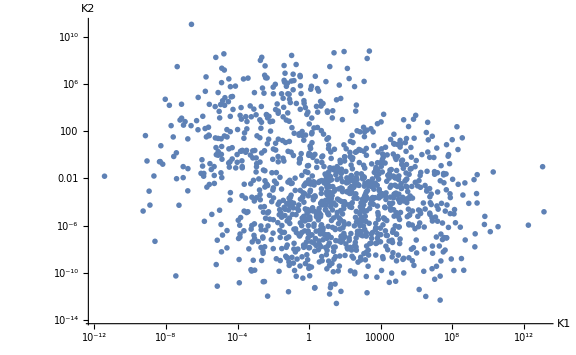

```mathematica
ListLogLogPlot[Transpose[{parK1,parK2}],AxesLabel->{"K1","K2"},ImageSize->Large]
```